```mathematica
(*Задание 1*)
```

```mathematica
(1-I^2)/(1+I)^2+3+I
```

3

```mathematica
(*Задание 2*)
```

```mathematica
z=Sqrt[3]-I;
(*Модуль r*)
r=Abs[z];

(*Аргумент theta*)
theta=Arg[z];

(*Тригонометрическая форма*)
trigForm=r (Cos[theta]+I*Sin[theta]);

(*Выводим результаты*)
{r,theta,trigForm}
```

{2,-π/6,2 (-ⅈ/2+(√3)/2)}

```mathematica
(*Задание 3*)
Clear[z]
Simplify[Select[Solve[-Sqrt[2]-I Sqrt[6]+z^3==0,z],!Element[z/. #1,Reals]&]]
```

{{z→(√2+ⅈ √6)^(1/3)},{z→-(-1)^(1/3) (√2+ⅈ √6)^(1/3)},{z→(-1)^(2/3) (√2+ⅈ √6)^(1/3)}}

```mathematica
(*Задание 4*)
(*Комплексное число*)z=1+I;

(*Модуль и аргумент*)
r=Abs[z];
theta=Arg[z];

(*Показательная форма*)
expForm=r Exp[I theta]

(*Выводим результаты*)
{r,theta,expForm}
```

√2 ⅇ^((ⅈ π)/4)

```mathematica
(*Задание 6*)
```

```mathematica
z=2-I;

	
sinZ=Sin[z];

(*Действительная и мнимая части*)
realPart=Re[sinZ];
imaginaryPart=Im[sinZ];

(*Выводим результаты*)
{ComplexExpand[realPart],ComplexExpand[imaginaryPart]}
```

{Cosh[1] Sin[2],-Cos[2] Sinh[1]}

```mathematica
(*Задание 5*)
```

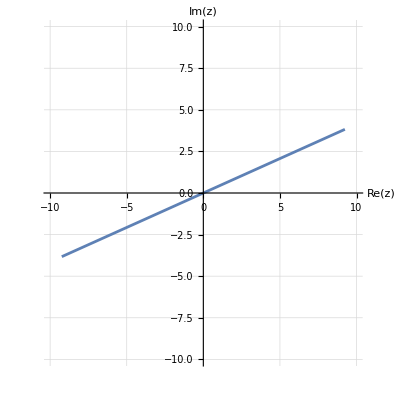

```mathematica
(*Параметрическое уравнение прямой*)θ=π/8;
t=Range[-10,10,0.1];
z=t*Exp[I θ];

(*Плоскость для отрисовки*)
ReImPlane={{-10,10},{-10,10}};

(*Построение графика*)
ListLinePlot[Transpose[{Re[z],Im[z]}],AxesLabel->{"Re(z)","Im(z)"},PlotRange->ReImPlane,GridLines->Automatic,AspectRatio->1]
```

```mathematica
(*Задание 7*)
(*Определяем действительную часть функции*)u[x_,y_]:=x^2-y^2+5 x

(*Находим частные производные u*)
ux[x_,y_]:=D[u[x,y],x]
uy[x_,y_]:=D[u[x,y],y]

(*Формулы Коши-Римана для нахождения v_y и интеграции по y*)
vy[x_,y_]:=ux[x,y]
v_int_y=Integrate[vy[x,y],y]+g[x]

(*По другому уравнению Коши-Римана находим-v_x и интегрируем по x*)
v[x_,y_]:=(2 x+5) y

(*Собираем общий вид комплексной функции f[z]*)
f[x_,y_]:=u[x,y]+I v[x,y]

(*Начальное условие f[0]=0*)
initialCondition=f[0,0]==0

(*Вычисляем f[z]*)
f[z_]:=ComplexExpand[u[Re[z],Im[z]]+I v[Re[z],Im[z]]]

(*Результат*)
f[x+I y]
```

Set::write: Tag Times in _y v_int is Protected.

5 y+2 x y+g[x]

True

5 x+x^2-y^2+ⅈ (5 y+2 x y)

```mathematica
(*Задание 8*)
Clear[y,x,dy]
y:=(1/4) x^2
dy:=D[y,x]
Print[dy]
```

x/2

```mathematica
(*Интеграция по x*)integral1=Integrate[x-y*dy,{x,0,2}] 

(*Интеграция по y с учетом выражения для dy*)
integral2=Integrate[y+dy*x,{x,0,2}] 

(*Финальный ответ*)
finalIntegral=integral1+I*integral2
Simplify[finalIntegral]
```

3/2

2

3/2+2 ⅈ

3/2+2 ⅈ

```mathematica
(*Задание 9*)
```

```mathematica
(*1. Определение функции*)
Clear[z]
f:=Sin[z]^2

(*2. Определение точки разрыва*)
pole=1;

(*3. Вычисление первой производной функции символически*)
fPrime=D[f,z]

fPrimeAtPole=fPrime/. z->pole

(*5. Используем теорему Коши для вычисления интеграла*)
integral=2*Pi*I*fPrimeAtPole
```

2 Cos[z] Sin[z]

2 Cos[1] Sin[1]

4 ⅈ π Cos[1] Sin[1]

```mathematica
(*Задание 11 тут надо ручками*)
(*Определяем функцию*)
f:=1/Sin[z]^3
Reduce[1/f==0,z]
Assuming[Element[C[1],Integers],Residue[f,{z,0 C[1]}]]
```

C[1]∈ℤ&&(z==2 π C[1]||z==π+2 π C[1])

```mathematica
1/2
```

```mathematica
(*Задание 12*)
(*Определяем функцию*)f:=(z^2+z+1)/(z^2*(z-1))

(*Найдем особые точки функции (знаменатель не должен быть ровен 0)*)
singularities=Solve[z^2*(z-1)==0,z]
singularPoints=z/. singularities

(*Функция для вычисления вычета*)
residueAtPoint[f,z_,z0_]:=Residue[f,{z,z0}]

(*Вычислим вычеты в каждой особой точке*)
residues=Table[{pts,residueAtPoint[f,z,pts]},{pts,singularPoints}]
```

{{z→0},{z→0},{z→1}}

{0,0,1}

{{0,-2},{0,-2},{1,3}}

```mathematica
(*Задание 13*)
integrand=Cot[z];


contour=Abs[z]==2;


residue=Residue[integrand,{z,0}];
Print[residue]

integral=2*Pi*I*residue
```

1

2 ⅈ π

```mathematica
(*Задание 10*)
f:=(z+2)/(z^2-4*z+3)


Series[f,{z,1,-1}]
```

-3/(2 (z-1))+O[z-1]^0